```mathematica
data = Import["/home/pi/PhyExam/Exp8/Exp8.xlsx"]
```

{{{S(cm),DeltaT(ms),,,v/(m/s),v^2,2s},{20.,37.17,37.67,37.26,0.253524,0.0642742,0.4},{30.,31.38,30.82,31.34,0.303827,0.092311,0.6},{40.,26.17,26.85,26.87,0.355739,0.12655,0.8},{50.,24.02,24.05,23.88,0.394997,0.156022,1.},{60.,21.82,21.97,22.05,0.431652,0.186324,1.2},{DeltaS,0.94,0.952,0.95,0.947333,,},{h,15.,15.08,15.,,,},{L,86.29,87.5,87.49,,,}},{{m2(g),172.4,172.33,172.3,172.343},{m1(g),333.14,333.18,333.17,333.163},{DeltaS,0.94,0.952,0.95,0.947333},{Exp1,,,,},{P1.1,16.51,21.11,17.35,},{P2.1,12.62,16.15,13.27,},{P2.2,52.71,66.83,55.67,},{v10,0.573794,0.44876,0.546013,},{v1,0.179726,0.141753,0.170169,},{v2,0.75066,0.586584,0.713891,},{DeltaP/P,0.0100318,0.00795841,0.0120008,},{DeltaE/E,0.0165458,0.0163924,0.0185799,},{e,0.995018,0.991245,0.995802,}},{{m2(g),172.4,172.33,172.3,172.343},{m1(g),333.14,333.18,333.17,333.163},{DeltaS,0.94,0.952,0.95,0.947333},{Exp1,,,,},{P1.1,14.41,18.2,13.16,},{P2.1,22.3,28.18,20.53,},{P2.2,22.36,28.3,20.6,},{v10,0.657414,0.520513,0.719858,},{v1,0.423673,0.334747,0.459871,},{v2,0.424813,0.336172,0.461439,},{DeltaP/P,0.0212764,0.0227972,0.0295729,},{DeltaE/E,0.368678,0.370637,0.379335,},{e,0.00173396,0.00273858,0.0021782,}},{{m2(g),172.4,172.33,172.3,172.343},{m1(g),333.14,333.18,333.17,333.163},{DeltaS,0.94,0.952,0.95,0.947333},{Exp1,,,,},{P1.1,17.68,15.19,14.89,},{P2.1,22.48,15.82,15.38,},{P2.2,32.13,34.77,32.85,},{v10,0.535822,0.623656,0.636221,},{v1,0.294844,0.272457,0.288382,},{v2,0.421412,0.59882,0.615951,},{DeltaP/P,0.0428958,0.0664355,0.0459145,},{DeltaE/E,0.377239,0.33223,0.309687,},{e,0.236212,0.523306,0.514868,}}}

```mathematica
fitData = data[[1]][[2;;6,{-1,-2}]]
deltaS = data[[1]][[7,-3]]
h = data[[1]][[8,2;;4]]*10^-2
l = data[[1]][[9,2;;4]]*10^-2
ft = LinearModelFit[fitData,{x},{x}]
```

{{0.4,0.0642742},{0.6,0.092311},{0.8,0.12655},{1.,0.156022},{1.2,0.186324}}

0.947333

{0.15,0.1508,0.15}

{0.8629,0.875,0.8749}

FittedModel[0.00197212+0.153905 x]

```mathematica
%["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00197212 | 0.00202166 | 0.975498 | 0.401258
x | 0.153905 | 0.00238255 | 64.597 | 8.17448×10^-6

```mathematica
line = Fit[fitData,{1,x},x]
```

0.00197212+0.153905 x

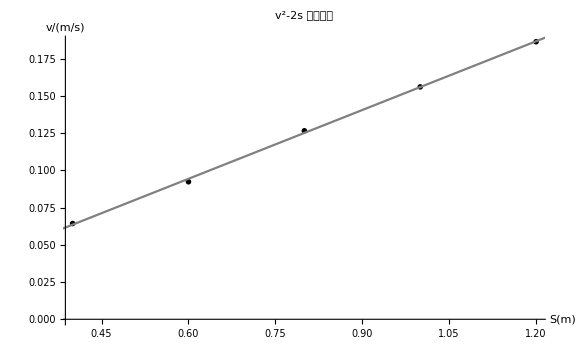

```mathematica
Show[ListPlot[fitData, PlotStyle->Black,PlotMarkers->{Style["X",10]}],Plot[line, {x,0, 1.5},PlotStyle->Gray],AxesLabel->{Style["S(m)",15,Bold],Style["v/(m/s)",15,Bold]},
PlotLabel->Style["v^2-2s  拟合曲线",18,FontFamily->"Adobe Fan Heiti Std", Bold],
AxesStyle->Directive[Arrowheads[0.05],13],
ImageSize->Large]
```

```mathematica
sintheta = Mean[h]*0.1/Mean[l]
```

0.0172535

```mathematica
g = ft["BestFitParameters"][[2]]/sintheta
```

8.92022